# RPV Gluino Reach

by Flip Tanedo, 7 August 2012

Generates reach plot for SS2L RPV gluino search. SR8 only, just a proof of principle of my code. (Many thanks for Mike Saelim.)

```mathematica
ClearAll["Global`*"]
```

## Import List of K-factors, NLO cross sections

K-factors and NLO cross sections are calculated in Prospino and are stored as a function for rescaling events.

### K factors (don’t need to use this if you’re using NLO Cross Sections)

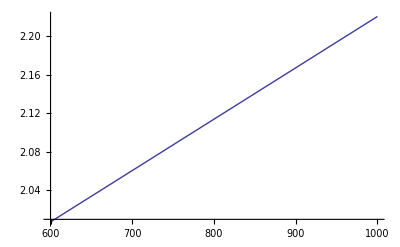

```mathematica
Prospino=Import["/Users/fliptomato/Documents/Code/RPVgluino/KfactorList.txt","Table"];
KFactor[x_]=Fit[Prospino,{1,x},x]; (* Note use of immediate definition vs delayed definition := *)
(* I knew from looking at the data that a linear fit is appropriate *)

Plot[KFactor[x],{x,600,1000}]
```

### NLO Cross Sections

```mathematica
ProspinoXSec=Import["/Users/fliptomato/Documents/Code/RPVgluino/NLOsigma.txt","Table"];
FirstAndThird[x_]:={x[[1]],x[[3]]}
(* Second element is LO cross section *)
NLOXSec = FirstAndThird/@ProspinoXSec;
```

```mathematica
NLOSig=Interpolation[NLOXSec]
```

InterpolatingFunction[{{600.,800.}},<>]

## Import Signal Efficiency Data

```mathematica
SignalEfficiency = Import["/Users/fliptomato/Documents/Code/RPVgluino/output_07Aug.dat","Table"];

(* A useful function for dropping the Signal Region info *)
(* Also, re-order so that mgluino comes before mtop *)
DropThirdElement[x_]:={x[[2]],x[[1]],x[[4]]};

(* This is now a list of elements with format {x,y,f(x,y)} *)
SignalEffData = DropThirdElement/@SignalEfficiency;
```

### Visualize

```mathematica
ListPlot3D[SignalEffData]
```

-Graphics3D-

## Get number of events

Multiply by signal efficiency by cross section and luminosity.

```mathematica
Lumi = 3.95/fb;
fb = 10^-3; (* cross sections are given in pb *)
Wlep = (0.3257)^2 ;(* additional factor fo forcing leptonic W decays *)
NSigEvents[x_]:={x[[1]],x[[2]],Wlep Lumi NLOSig[x[[1]]] x[[3]]}
NSignal=NSigEvents/@SignalEffData;
```

Be sure to double check whether the current Monte Carlo code includes a prefactor for leptonic W decays or not.

## Visualize

```mathematica
ListPlot3D[NSignal]
```

-Graphics3D-

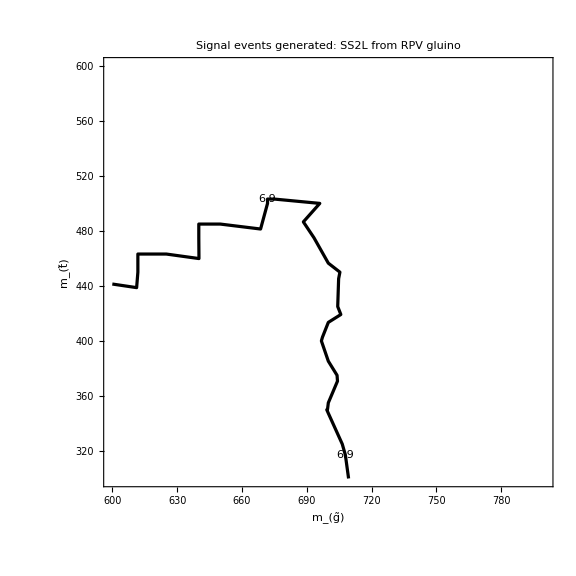

```mathematica
ListContourPlot[NSignal,
ContourLabels->All,
PlotLabel->"Signal events generated: SS2L from RPV gluino",
FrameLabel->{"m_(g̃)","m_(t̃)"},
ImageSize->Large,
(* Pick out stuff *)
Contours->{6.9}, (* From SUS-12-017 , Table 2 *)
ContourShading->None,
ContourStyle->{Thickness[0.004]}
]
```